```mathematica
<<Combinatorica`;
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
n=5;
DerivativeOrder=3;
StencilType=1;

(*Stencil Points*)
StencilPoints=GenStencilPoints[n,StencilType];
sys={StencilPoints,DerivativeOrder,n};
(*Plot Stencil
If[n==2,ListPlot[Append[StencilPoints,Table[0,{i,n}]],PlotMarkers->Automatic]]
If[n==3,ListPointPlot3D[Append[StencilPoints,Table[0,{i,n}]],PlotStyle->PointSize[Medium]]]*)
StencilPoints

(*Result*)
{a,res}=GenWeights[sys]

CheckWeights[res,sys]//N
```

{{1,0,0,0,0},{-1,0,0,0,0},{0,1,0,0,0},{0,-1,0,0,0},{0,0,1,0,0},{0,0,-1,0,0},{0,0,0,1,0},{0,0,0,-1,0},{0,0,0,0,1},{0,0,0,0,-1},{1,1,0,0,0},{-1,-1,0,0,0},{1,0,1,0,0},{-1,0,-1,0,0},{1,0,0,1,0},{-1,0,0,-1,0},{1,0,0,0,1},{-1,0,0,0,-1},{0,1,1,0,0},{0,-1,-1,0,0},{0,1,0,1,0},{0,-1,0,-1,0},{0,1,0,0,1},{0,-1,0,0,-1},{0,0,1,1,0},{0,0,-1,-1,0},{0,0,1,0,1},{0,0,-1,0,-1},{0,0,0,1,1},{0,0,0,-1,-1}}

{0.0409433,{3700.8,3672.,3700.8,3672.,3700.8,3672.,3700.8,3672.,3700.8,3672.,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4}}

Norm: 0.0409433

LS-Norm: 0.0409433

{3700.8,3672.,3700.8,3672.,3700.8,3672.,3700.8,3672.,3700.8,3672.,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4,3686.4}

```mathematica
Plot3D[PDECoefMatrix[{x,y}][[1,1]],{x,50,150},{y,50,150}]
```

-Graphics3D-

```mathematica
a=PDECoefMatrix[{x,y}]
```

{{0.02 x^2,0.018 x y},{0.018 x y,0.02 y^2}}

```mathematica
StencilPoints
```

{{1,0},{-1,0},{0,1},{0,-1},{1,1},{-1,-1}}

```mathematica
w=.
```

```mathematica
nn=100;
```

```mathematica
{res,wei}=GenDiagonals[sys,w];
```

```mathematica
Max[res]
```

1.60379

```mathematica
m=SplitOperator[wei,1,2,StencilPoints[[1]],indices];m//MatrixForm
```

(«1»)

```mathematica
q=m[[80,2]];t=SparseArray[{{i_,j_}/;Abs[i-j]≤1:>q[[i,j-i+2]]},{nn,nn}];t//MatrixForm;
```

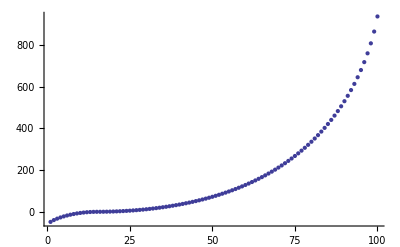

```mathematica
ListPlot[#,PlotRange->{Min[0,Min[#]],Max[#]}]&[Sort[-Eigenvalues[t]]]
```

```mathematica
m=SplitOperator[wei,3,4,StencilPoints[[3]],indices];m//MatrixForm
```

({1,1} | {{0.359677,-0.73,0.360323},{0.559623,-1.13,0.560377},{0.79957,-1.61,0.80043},{1.07952,-2.17,1.08048},{1.39946,-2.81,1.40054},{1.75941,-3.53,1.76059},{2.15935,-4.33,2.16065},{2.5993,-5.21,2.6007},{3.07925,-6.17,3.08075},{3.59919,-7.21,3.60081}}
{2,1} | {{0.299677,-0.61,0.300323},{0.489623,-0.99,0.490377},{0.71957,-1.45,0.72043},{0.989516,-1.99,0.990484},{1.29946,-2.61,1.30054},{1.64941,-3.31,1.65059},{2.03935,-4.09,2.04065},{2.4693,-4.95,2.4707},{2.93925,-5.89,2.94075},{3.44919,-6.91,3.45081}}
{3,1} | {{0.239677,-0.49,0.240323},{0.419623,-0.85,0.420377},{0.63957,-1.29,0.64043},{0.899516,-1.81,0.900484},{1.19946,-2.41,1.20054},{1.53941,-3.09,1.54059},{1.91935,-3.85,1.92065},{2.3393,-4.69,2.3407},{2.79925,-5.61,2.80075},{3.29919,-6.61,3.30081}}
{4,1} | {{0.179677,-0.37,0.180323},{0.349623,-0.71,0.350377},{0.55957,-1.13,0.56043},{0.809516,-1.63,0.810484},{1.09946,-2.21,1.10054},{1.42941,-2.87,1.43059},{1.79935,-3.61,1.80065},{2.2093,-4.43,2.2107},{2.65925,-5.33,2.66075},{3.14919,-6.31,3.15081}}
{5,1} | {{0.119677,-0.25,0.120323},{0.279623,-0.57,0.280377},{0.47957,-0.97,0.48043},{0.719516,-1.45,0.720484},{0.999462,-2.01,1.00054},{1.31941,-2.65,1.32059},{1.67935,-3.37,1.68065},{2.0793,-4.17,2.0807},{2.51925,-5.05,2.52075},{2.99919,-6.01,3.00081}}
{6,1} | {{0.0596772,-0.13,0.0603228},{0.209623,-0.43,0.210377},{0.39957,-0.81,0.40043},{0.629516,-1.27,0.630484},{0.899462,-1.81,0.900538},{1.20941,-2.43,1.21059},{1.55935,-3.13,1.56065},{1.9493,-3.91,1.9507},{2.37925,-4.77,2.38075},{2.84919,-5.71,2.85081}}
{7,1} | {{-0.000322838,-0.01,0.000322838},{0.139623,-0.29,0.140377},{0.31957,-0.65,0.32043},{0.539516,-1.09,0.540484},{0.799462,-1.61,0.800538},{1.09941,-2.21,1.10059},{1.43935,-2.89,1.44065},{1.8193,-3.65,1.8207},{2.23925,-4.49,2.24075},{2.69919,-5.41,2.70081}}
{8,1} | {{-0.0603228,0.11,-0.0596772},{0.0696234,-0.15,0.0703766},{0.23957,-0.49,0.24043},{0.449516,-0.91,0.450484},{0.699462,-1.41,0.700538},{0.989408,-1.99,0.990592},{1.31935,-2.65,1.32065},{1.6893,-3.39,1.6907},{2.09925,-4.21,2.10075},{2.54919,-5.11,2.55081}}
{9,1} | {{-0.120323,0.23,-0.119677},{-0.000376644,-0.01,0.000376644},{0.15957,-0.33,0.16043},{0.359516,-0.73,0.360484},{0.599462,-1.21,0.600538},{0.879408,-1.77,0.880592},{1.19935,-2.41,1.20065},{1.5593,-3.13,1.5607},{1.95925,-3.93,1.96075},{2.39919,-4.81,2.40081}}
{10,1} | {{-0.180323,0.35,-0.179677},{-0.0703766,0.13,-0.0696234},{0.0795695,-0.17,0.0804305},{0.269516,-0.55,0.270484},{0.499462,-1.01,0.500538},{0.769408,-1.55,0.770592},{1.07935,-2.17,1.08065},{1.4293,-2.87,1.4307},{1.81925,-3.65,1.82075},{2.24919,-4.51,2.25081}})

```mathematica
q=m[[9,2]];t=SparseArray[{{i_,j_}/;Abs[i-j]≤1:>q[[i,j-i+2]]},{10,10}]//MatrixForm
```

(0.23 | -0.119677 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000376644 | -0.01 | 0.000376644 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.15957 | -0.33 | 0.16043 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.359516 | -0.73 | 0.360484 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.599462 | -1.21 | 0.600538 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.879408 | -1.77 | 0.880592 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.19935 | -2.41 | 1.20065 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.5593 | -3.13 | 1.5607 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.95925 | -3.93 | 1.96075
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.39919 | -4.81)

```mathematica
Max[res]
```

6.35254

```mathematica
indices=Transpose[Reverse[Transpose[Tuples[Table[i,{i,100}],n]]]]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},«9940»,{71,100},{72,100},{73,100},{74,100},{75,100},{76,100},{77,100},{78,100},{79,100},{80,100},{81,100},{82,100},{83,100},{84,100},{85,100},{86,100},{87,100},{88,100},{89,100},{90,100},{91,100},{92,100},{93,100},{94,100},{95,100},{96,100},{97,100},{98,100},{99,100},{100,100}}